# FIR Filters

## Testy w Mathematica

```mathematica
FilterFunc[x_]:=UnitStep[-x+1/4];(*Exp[-1000(x-0.2)^2];*)
Manipulate[
fparams={1, -1}; (*params for DSP*)
n=512;dx=1./(n-1);
(*a=Table[UnitStep[-x+1/4],{x,0,1,dx}];*)
(*a=Table[If[x≤1/2,Exp[-100x^2],Exp[-100(1-x)^2]],{x,0,1,dx}];*)
b=Table[FilterFunc[x],{x,0,1,dx}];
a=Join[b,Conjugate[Reverse[Drop[b,1]]]];
siga=Table[Sin[1u(x)],{x,0,1,dx}];
sigb=Table[Sin[2u (x)],{x,0,1,dx}];
sigc=Table[Sin[8u (x)],{x,0,1,dx}];
coefMathInv=InverseFourier[a, FourierParameters->fparams][[1;;n]];
coefMath=Fourier[a, FourierParameters->fparams][[1;;n]];
filteredA=Chop@ListConvolve[coefMathInv[[1;;n/2]],siga];
filteredB=Chop@ListConvolve[coefMathInv[[1;;n/2]],sigb];
filteredC=Chop@ListConvolve[coefMathInv[[1;;n/2]],sigc];
{{ListPlot[a,Filling->Axis, ImageSize->Medium, PlotRange->All],
ListPlot[{siga,sigb,sigc},Filling->Axis,PlotLegends->{"1x","2x","8x"}, PlotRange->{{0,n},{-1,1}},ImageSize->Medium]},{ListPlot[{Chop@coefMath},Filling->Axis, ImageSize->Medium, PlotRange->All,PlotLabel->"Fourier"],
ListPlot[{Chop@coefMathInv},Filling->Axis, ImageSize->Medium, PlotRange->All,PlotLabel->"Inverse Fourier"],
ListPlot[{filteredA,filteredB,filteredC}, PlotRange->{{0,n},{-1,1}},Filling->Axis,ImageSize->Medium,PlotLegends->{"1x","2x","8x"}]}}
,{{u,8,"mulitplier"},8,100},SynchronousUpdating->False]
```

### Odtwarzanie transmitancji

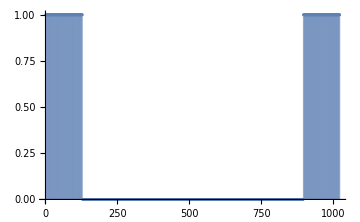

```mathematica
ListPlot[Chop@Fourier[InverseFourier[a, FourierParameters->fparams], FourierParameters->fparams],PlotRange->Full,ImageSize->Medium, Filling->Axis]
```

## Wyniki z C

```mathematica
ImportComplex[name_]:=Import[name,"Data"][[All,3]]+ⅈ Import[name,"Data"][[All,4]];
```

### Porównanie współczynników double i fixed point w C

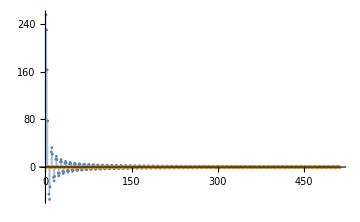
{-Graphics-,-Graphics-}

```mathematica
coefs=ImportComplex["coefs.dat"];
coefsReal=ImportComplex["coefsReal.dat"];
{ListPlot[{Re@coefs,Im@coefs},PlotRange->Full, Filling->Axis,ImageSize->Medium],
ListPlot[{Re@coefsReal,Im@coefsReal},PlotRange->Full, Filling->Axis,ImageSize->Medium]}
```

#### Różnica pomiędzy współczynnikami double i fixed point w C

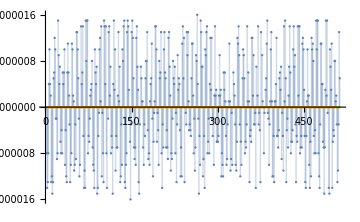

```mathematica
ListPlot[{Re@coefsReal-Re@coefs,Im@coefsReal-Im@coefs},PlotRange->Full, Filling->Axis,ImageSize->Medium]
```

#### Różnica między współczynnikami double i z Mathematica

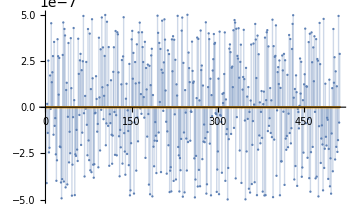

```mathematica
ListPlot[{Re@coefMath-Re@coefs,Im@coefMath-Im@coefs},PlotRange->Full, Filling->Axis,ImageSize->Medium]
```

### Transmitancja obliczona dla współczynników double i fixed point

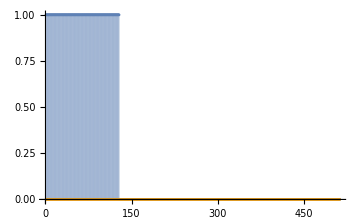
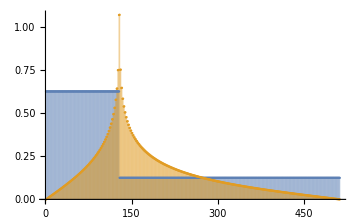

```mathematica
TF=ImportComplex["TransferF.dat"];
TFR=ImportComplex["TransferFReal.dat"];
{ListPlot[{Re@TF,Im@TF}/(2n-1),PlotRange->Full, Filling->Axis,ImageSize->Medium],
ListPlot[{Re@TFR,Im@TFR}/(2n-1),PlotRange->Full, Filling->Axis,ImageSize->Medium]}
```

Skąd aż taka różnica?
Patrząc poniżej wygląda na to, że KISS FTT robi jakiś trik wykonując odwrotną FTT

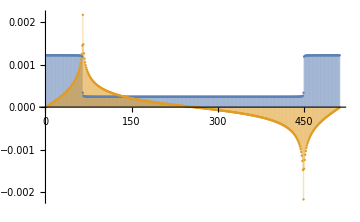
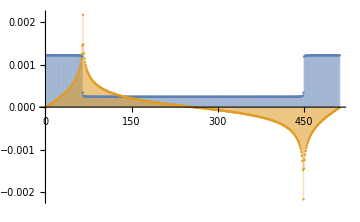

```mathematica
fp={1,-1};
{ListPlot[{Re@InverseFourier[coefs/(2n-1), FourierParameters->fp],Im@InverseFourier[coefs/(2n-1), FourierParameters->fp]},PlotRange->Full,ImageSize->Medium, Filling->Axis],
ListPlot[{Re@InverseFourier[coefsReal/(2n-1), FourierParameters->fp],Im@InverseFourier[coefsReal/(2n-1), FourierParameters->fp]},PlotRange->Full,ImageSize->Medium, Filling->Axis]}
```

1